#### Lattice depth and potential envelopes

As a function of distance along 111 the lattice depth is

```mathematica
vL111[ r_,s0_,w_]:=s0 Exp[- (4 r^2)/(3 w^2)]
```

This is also the envelope for the bottom of the potential

For the compensationg potential we have  the same equation

```mathematica
vC111[r_,g0_,w_]:=g0 Exp[- (4 r^2)/(3 w^2)]
```

#### Bands as a function of lattice depth

With the lattice depth in hand we can calulate the bottom of the band.  For this we use the energy of the harmonic oscillator state,  with a polinomial correction.  The polynomial correction coefficients were calculated in  an IPython notebook called BandsPolyfit

```mathematica
b00=-1.5032;
b01=5.8301*^-2;
b02=-3.9164*^-4;
b03=-5.9045*^-5;
b04=1.108*^-6;
bot0[ s_] := 3. √s+b00 +b01 s+b02 s^2+b03 s^3+b04 s^4

t00=+3.0057;
t01=+7.4294*^-1;
t02=-2.1721*^-2;
t03=+6.0294*^-4;
t04=-9.9790*^-6;
t05=+7.0144*^-8;
top0[ s_] := t00 +t01 s+t02 s^2+t03 s^3+t04 s^4+t05 s^5

b10=-1.2629;
b11=+4.9235*^-2;
b12=+1.8631*^-2;
b13=-7.8060*^-4;
b14=+9.3920*^-6;
bot1[ s_] := (3.+1) √s+b10 +b11 s+b12 s^2+b13 s^3+b14 s^4 

t10=+6.0027;
t11=+9.9644*^-1;
t12=-1.9971*^-2;
t13=+4.2764*^-4;
t14=-6.0709*^-6;
t15=+3.9194*^-8;
top1[ s_] := t10 +t11 s+t12 s^2+t13 s^3+t14 s^4+t15 s^5
```

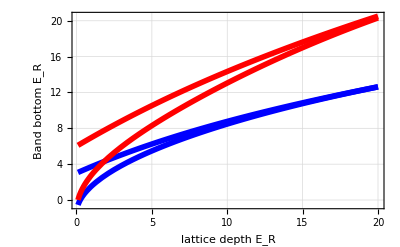

```mathematica
Plot[ {bot0[s], top0[s],bot1[s],top1[s]},{s,0.1,20}, Frame->True, PlotStyle->{
{Thickness[0.01],Blue},
{Thickness[0.01],Blue},
{Thickness[0.01],Red},
{Thickness[0.01],Red}
},
FrameLabel->{"lattice depth E_R","Band bottom E_R"},FrameStyle->Directive[18],GridLines->Automatic]
```

### Tunneling rate and onsite interactions as a function of lattice depth and scattering length

```mathematica
tunneling[s_]:=Module[{λ},
λ=(1064*^-9)/(5.29*^-11); (*express the lattice wavelength in units of Bohr radius*)

(*Return the tunneling in recoils*)
4 π^(-1/2)  s^(3/4)Exp[-2 √s] ]



onsite[s_,as_]:=Module[{λ},
λ=(1064*^-9)/(5.29*^-11); (*express the lattice wavelength in units of Bohr radius*)

(*Return the onsite interaction in recoils*)
4 √2 π^(1/2)as/λ s^(3/4)]

onsitet[s_,as_]:=Module[{λ},
λ=(1064*^-9)/(5.29*^-11); (*express the lattice wavelength in units of Bohr radius*)
π √2. as/λ Exp[2 √s]]
```

```mathematica
onsite[7.,650.]
tunneling[7.]
onsitet[7.,650.]
```

1.39444

0.048892

28.5209

### Reproduce Mathy Fig. 4a (without compensation)

1005.67

2.15746

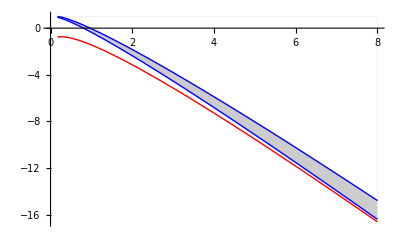

```mathematica
s0=8.;
wL=47.;
bandbot=Table[ {vL111[r,s0,wL],  -3 vL111[r,s0,wL]+bot0[vL111[r,s0,wL]]},{r,0,80,1}];
bandmid=Table[ {vL111[r,s0,wL],  -3 vL111[r,s0,wL]+(bot0[vL111[r,s0,wL]]+top0[vL111[r,s0,wL]])/2.},{r,0,80,1}];

(*Mathy likes to give the scattering length in units of the lattice spacing*)
asLatt = 0.1; 
as=asLatt  (532*^-9)/(5.29*^-11)
onsite[vL111[0.,7.,47.],as]

bandmidPlusU=Table[ {vL111[r,8.,47.],  -3 vL111[r,8.,47.]+(bot0[vL111[r,7.,47.]]+top0[vL111[r,7.,47.]])/2.+onsite[vL111[r,7.,47.],as]},{r,0,80,1}];

ListLinePlot[{bandbot ,bandmid, bandmidPlusU},PlotStyle->{Red,Blue,Blue},
Filling->{
2->{1.,{Opacity[0.2],Hue[0.67,0.6,0.6]}},
3->{1.,{White}}
}]
```

### Reproduce Mathy Fig. 5a (with compensation)

8.

5.39256

1005.67

2.15746

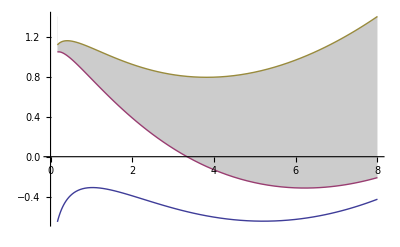

```mathematica
beta = 0.379;
alpha=1.13;
s0 = 8.
g0 = beta (s0)^(alpha^2)

wL = 47.;
wC = wL/alpha;

bandbot=Table[ {vL111[r,s0,wL],  3.vC111[r,g0,wC]-3 vL111[r,s0,wL]+bot0[vL111[r,s0,wL]]},{r,0,80,1}];
bandmid=Table[ {vL111[r,s0,wL],  3.vC111[r,g0,wC]-3 vL111[r,s0,wL]+(bot0[vL111[r,s0,wL]]+top0[vL111[r,s0,wL]])/2.},{r,0,80,1}];

(*Mathy likes to give the scattering length in units of the lattice spacing*)
asLatt = 0.1; 
as=asLatt  (532*^-9)/(5.29*^-11)
onsite[vL111[0.,7.,47.],as]

bandmidPlusU=Table[ {vL111[r,8.,47.],  3.vC111[r,g0,wC]-3 vL111[r,8.,47.]+(bot0[vL111[r,7.,47.]]+top0[vL111[r,7.,47.]])/2.+onsite[vL111[r,7.,47.],as]},{r,0,80,1}];

ListLinePlot[{bandbot ,bandmid, bandmidPlusU},Filling->{
2->{1.4,{Opacity[0.2],Hue[0.67,0.6,0.6]}},
3->{3.,{White}}
}]
```

### Make Mathy Fig. 5a for equal beam waists

8.

5.33632

1005.67

2.15746

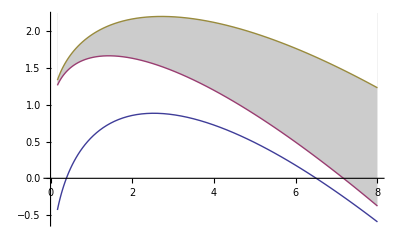

```mathematica
beta = 0.379;
alpha=1.00;
s0 = 8.
g0 = 1.76beta (s0)^(alpha^2)

wL = 47.;
wC = wL/alpha;

bandbot=Table[ {vL111[r,s0,wL],  3.vC111[r,g0,wC]-3 vL111[r,s0,wL]+bot0[vL111[r,s0,wL]]},{r,0,80,1}];
bandmid=Table[ {vL111[r,s0,wL],  3.vC111[r,g0,wC]-3 vL111[r,s0,wL]+(bot0[vL111[r,s0,wL]]+top0[vL111[r,s0,wL]])/2.},{r,0,80,1}];

(*Mathy likes to give the scattering length in units of the lattice spacing*)
asLatt = 0.1; 
as=asLatt  (532*^-9)/(5.29*^-11)
onsite[vL111[0.,7.,47.],as]

bandmidPlusU=Table[ {vL111[r,8.,47.],  3.vC111[r,g0,wC]-3 vL111[r,8.,47.]+(bot0[vL111[r,7.,47.]]+top0[vL111[r,7.,47.]])/2.+onsite[vL111[r,7.,47.],as]},{r,0,80,1}];

ListLinePlot[{bandbot ,bandmid, bandmidPlusU},Filling->{
2->{2.25,{Opacity[0.2],Hue[0.67,0.6,0.6]}},
3->{3.,{White}}
}]
```

### It seems that this plots will not really help me get my point across, that having equal beam waists is not that bad as far as the Mott plateau goes. Maybe where I am getting it wrong is in keeping the atom number at 350,000. With the smaller beam waist the system can be compensated to tolerate more atoms. This is something that I need to investigate with the python code, for example make a plot of max atom number vs. beam waist ratio.

## Investigation of the effects of the lock. As a function of beam waist, at what point does the lock start getting in to higher band territory.

#### Get the solution using the band polynomial approximation:

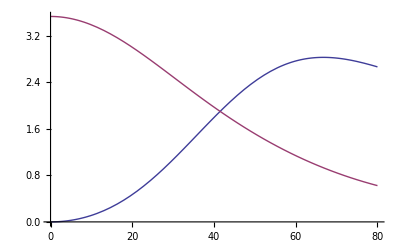

```mathematica
s0=7.;
g0=3.6;
wC=40.;
wL=47.;
Plot[ {
  3.vC111[r,g0,wC]-3 vL111[r,s0,wL]+bot0[vL111[r,s0,wL]] - (3.vC111[0.,g0,wC]-3 vL111[0.,s0,wL]+bot0[vL111[0.,s0,wL]]),
bot1[vL111[r,s0,wL]]-bot0[vL111[r,s0,wL]]
},{r,0,80}]
```

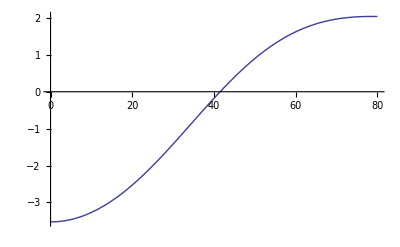

```mathematica
Plot[ {
  3.vC111[r,g0,wC]-3 vL111[r,s0,wL]+bot0[vL111[r,s0,wL]] - (3.vC111[0.,g0,wC]-3 vL111[0.,s0,wL]+bot0[vL111[0.,s0,wL]])-(
bot1[vL111[r,s0,wL]]-bot0[vL111[r,s0,wL]])
},{r,0,80}]
```

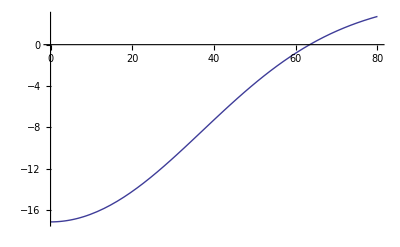

```mathematica
Plot[3.vC111[r,g0,wC]-3 vL111[r,s0,wL]+bot0[vL111[r,s0,wL]] - (3.vC111[0.,g0,wC]-3 vL111[0.,s0,wL]+bot0[vL111[0.,s0,wL]])-
bot1[vL111[r,s0,wL]]-bot0[vL111[r,s0,wL]], {r,0,80}]
```

```mathematica
bandRadius[s0_,g0_]:=Module[ {wC,wL},
wC=40.;
wL=47.;
r/.FindRoot[     3.vC111[r,g0,wC]-3 vL111[r,s0,wL]+bot0[vL111[r,s0,wL]] - (3.vC111[0.,g0,wC]-3 vL111[0.,s0,wL]+bot0[vL111[0.,s0,wL]])-(
bot1[vL111[r,s0,wL]]-bot0[vL111[r,s0,wL]]),{r,35.}]
]
```

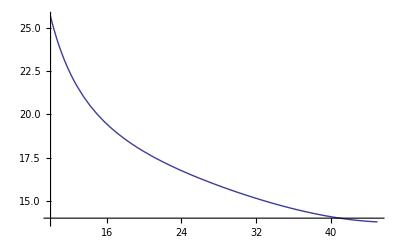

```mathematica
Plot[bandRadius[s0,3.6],{s0,10.,45.}]
```

#### Get the solution using h. osc states

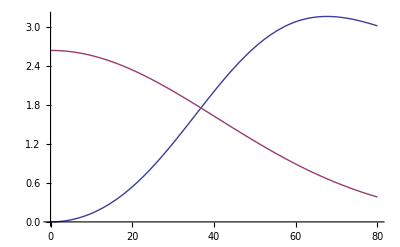

```mathematica
s0=7.;
g0=3.6;
wC=40.;
wL=47.;
Plot[ {
  3.vC111[r,g0,wC]-3 vL111[r,s0,wL]+3. √vL111[r,s0,wL]- (3.vC111[0.,g0,wC]-3 vL111[0.,s0,wL]+3. √vL111[0.,s0,wL]),
√vL111[r,s0,wL]
},{r,0,80}]
```

```mathematica
bandRadiusHOSC[s0_,g0_]:=Module[ {wC,wL},
wC=40.;
wL=47.;
r/.FindRoot[  3.vC111[r,g0,wC]-3 vL111[r,s0,wL]+3. √vL111[r,s0,wL]- (3.vC111[0.,g0,wC]-3 vL111[0.,s0,wL]+3. √vL111[0.,s0,wL])-
√vL111[r,s0,wL],{r,10.}]
]
bandRadiusHOSC[7.,3.6]
```

36.8016

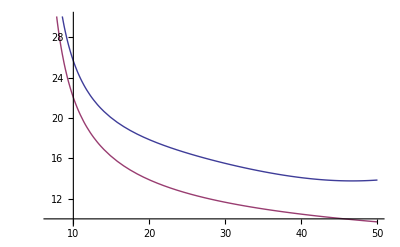

```mathematica
Plot[{bandRadius[s0,3.6],bandRadiusHOSC[s0,3.6]},{s0,7.,50.}]
```

### Other stuff

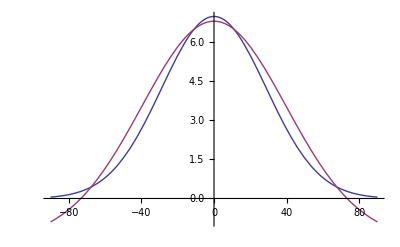

```mathematica
Plot[  { vL111[r,7.,47.],bot[vL111[r,7.,47.]]}, {r,-90,90}]
```